## Curso do Mathematica

Elementos do Mathematica

Operações com Matrizes

Gráficos e Animações

Cálculo e Equações Diferenciais

Programação Elementar no Mathematica

Tratamento de Dados e Imagens

Programação Funcional

Programação Baseada em Padrões

◀     |     ▶

## Paradigmas Computacionais

Paradigma Estruturado (C, Fortran)

Paradigma Orientação Objeto (C++, Java)

Paradigma Funcional (Lisp, Mathematica)

## Compilação

Linguagens Compiladas (C, Fortran, C++)

Linguagens não compiladas (Python, Mathematica, JavaScript)

Linguagem com Máquina Virtual

## Elementos do Mathematica

O Mathematica funciona como um editor de texto, ele substitui padrões textuais por outros padrões textuais.

O Mantra é "No Mathematica tudo são Expressões"

◀     |     ▶

## Imagem

O Mathematica é um editor de texto gigante que transforma expressões em expressões de forma iterativa.

## Entrada e Saída

O principal tipo de célula são as células de entrada, elas podem executar operações e gerar ou não saída. 
Em geral uma saída é produzida a menos que se coloque um ";" no final.

◀     |     ▶

## Acessando o Help

Através do Menu Help

Usando ?Plot (Informações sobre o Plot)

Usando ?*Image* (Informaçãoes sobre Funções que contenam a String “Image”

## Digitação

Para executar um Comando Shift-Enter (ou o enter do Teclado Numérico)

Cuidado com Maiúsculas e Minúsculas

[ ] Colchetes

{ } Chaves

## Atribuindo valores

Atribuição atualizada de valores:

```mathematica
chonga=2;
baranga=chonga;
baranga
chonga=3;
baranga
```

2

2

◀     |     ▶

## Atribuição Postergada

```mathematica
chonga:=baranga;
baranga=2;
chonga
baranga=3;
chonga
```

2

3

◀     |     ▶

## Funções

Funções no Mathematica são regras de transformação. Elas procuram por padrões e executam substituições.

```mathematica
f[x_]:=x^2;
```

```mathematica
f[2]
f[2.]
f[cachorro]
f[I]
2//f (* Uma maneira diferente de dizer a mesma coisa *)
```

4

4.

cachorro^2

-1

F[2]

◀     |     ▶

## Tipos

Inteiros

Reais

Complexos

Strings

Expressões

◀     |     ▶

## Restingindo Funções

```mathematica
fact[n_Integer]:=n!
```

```mathematica
fact[7]
fact[7.1]
```

5040

fact[7.1]

```mathematica
fact[x_Real]=Gamma[x+1];
```

```mathematica
fact[7.1]
fact[7.]
```

6169.59

5040.

◀     |     ▶

## Funções com muitas variáveis

f[x_,y_,z_]=x*x+y*y+z*z;


f[1,1,1]
3
◀     |     ▶

## Exercício

Construa uma função que calcule o volume de um paralelepído de lados a,b e c. Construa uma função que calcule a área lateral do mesmo paralelepipido.

Construa uma função que calcule o módulo de um número real. Generalize para o caso de um número Complexo. Como se calcula o conjugado de um número Complexo? Use o help para buscar alternativas.

Implemente uma função que conte o número de algarismos pares em um número natural.

Inplemente a função sucessor: Ela transforma uma string formada ppr “|||| ... |||” e adiciona um “|” extra.

◀     |     ▶

## Exercício

Construa uma função que tomando como entrada 
a, b e c e calcule o número de raízes da equação de segundo grau; ax^2+bx+c=0. Descubra como funciona o comando If.

◀     |     ▶

## Listas

No Mathematica o uso de listas é muito flexível.

```mathematica
lista={1,2,3};
lista+lista
Sin[lista]
```

{2,4,6}

{Sin[1],Sin[2],Sin[3]}

◀     |     ▶

## Listas

Os elementos de uma lista podem ser quase qualquer coisa, até mesmo outras listas.

{1,2,{1,2}}

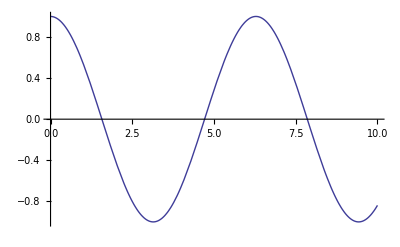
{1,Cos[x],banana,-Graphics-}

```mathematica
lista={1,2,{1,2}}
lista2={1,Cos[x],"banana",Plot[Cos[x],{x,0,10}]}
```

◀     |     ▶

## Acessando Elementos

```mathematica
lista
lista[[1]]
lista[[{1,2}]]
lista[[3,2]]
```

{1,2,{1,2}}

1

{1,2}

2

◀     |     ▶

## Funções Puras

```mathematica
f[x_]:=x ^2;
g:= #^2&;
h:=(#1^2+#2^3)&;
```

```mathematica
f[2]
g[2]
h[1,2]
```

4

4

9

◀     |     ▶

## Comandos em Listas

Table - Cria Listas

Append - Coloca Termos no Final de uma Lista

Prepend - Coloca Termos no Inicio de uma Lista

Sort - Ordena Lista

Take - Obtem Elementos de uma Lista

Select - Seleciona Elementos de uma Lista Baseado em Critérios

◀     |     ▶

## Exercício

Gere uma tabela contendo os números impares eselecione aqueles que são quadrados perfeitos.

◀     |     ▶

## Exercício

Gere uma Tabela contendo 1000 triplas de números inteiros aleatórios menores que 1000. Use o comando Random[]. 
Agora considere os polinomios formados utilizando
os valores aleatórios {a,b,c} na forma  a*x^2+b*x+c. E determine que fração deles possui duas raízes reais, 1 única raiz e duas raízes complexas.

◀     |     ▶

## Matrizes

No Mathematica Vetores e Matrizes são representados por Listas.

```mathematica
ve1={x,y};
ve2={u,v};
A={{a,b},{c,d}}
```

{{a,b},{c,d}}

```mathematica
{{a ,c},{b, d}}
```

{{a,c},{b,d}}

```mathematica
ve1.ve2
A.ve1
Det[A]
```

u x+v y

{a x+b y,c x+d y}

-b c+a d

◀     |     ▶

## Exemplos

```mathematica
A={{1,2},{3,4}};
Eigenvalues[A]
Eigenvectors[A]
Eigensystem[A]
```

◀     |     ▶

## Exercício

Gere 1000 matrizes aleatórias formados por inteiros 
menores do que 1000. Determine quantas matrizes possuem os dois autovalores reais, complexos e dois autovalores iguais.

◀     |     ▶

## Exercício

Crie uma função que calcule a Exponencial de uma Matriz. Existem várias formas de fazer isto. Faça da forma esperta. Se realmente você quiser se divertir
faça uma função que calcule a Tangente de uma 
matriz. 
Generalize sua função para que faça o cálculo da matriz de  qualquer função analítica.

◀     |     ▶